```mathematica
flogistic[t_,α_,ν_,κ_,y0_]:=κ/(1+((κ/y0)^ν - 1) Exp[-α ν t])^(1/ν)
```

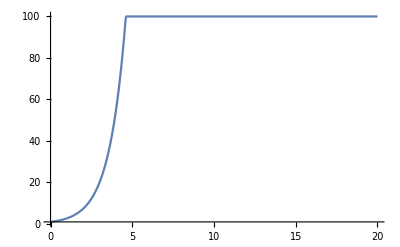

```mathematica
Plot[flogistic[t,1,100,100,1],{t,0,20},PlotRange->Full]
```

```mathematica
D[κ/(1+((κ/y0)^ν - 1) Exp[-α ν t])^(1/ν),α]
```

ⅇ^(-t α ν) t κ (-1+(κ/y0)^ν) (1+ⅇ^(-t α ν) (-1+(κ/y0)^ν))^(-1-1/ν)

```mathematica
falpha[t_,α_,ν_,κ_,y0_]:= ⅇ^(-t α ν) t κ (-1+(κ/y0)^ν) (1+ⅇ^(-t α ν) (-1+(κ/y0)^ν))^(-1-1/ν)
```

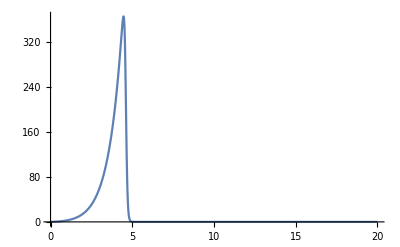

```mathematica
Plot[falpha[t,1,20,100,1],{t,0,20},PlotRange->Full]
```

```mathematica
D[κ/(1+((κ/y0)^ν - 1) Exp[-α ν t])^(1/ν),ν]//FullSimplify
```

1/ν^2 ⅇ^(-t α ν) κ (ⅇ^(-t α ν) (-1+ⅇ^(t α ν)+(κ/y0)^ν))^(-(1+ν)/ν) (t α (-1+(κ/y0)^ν) ν-(κ/y0)^ν ν Log[κ/y0]+(-1+ⅇ^(t α ν)+(κ/y0)^ν) Log[1+ⅇ^(-t α ν) (-1+(κ/y0)^ν)])

```mathematica
fν[t_,α_,ν_,κ_,y0_]:=1/ν^2 ⅇ^(-t α ν) κ (ⅇ^(-t α ν) (-1+ⅇ^(t α ν)+(κ/y0)^ν))^(-(1+ν)/ν) (t α (-1+(κ/y0)^ν) ν-(κ/y0)^ν ν Log[κ/y0]+(-1+ⅇ^(t α ν)+(κ/y0)^ν) Log[1+ⅇ^(-t α ν) (-1+(κ/y0)^ν)])
```

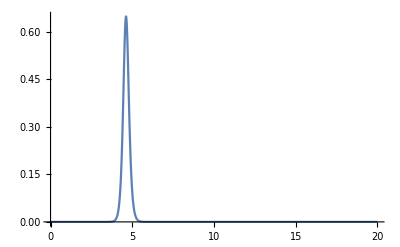

```mathematica
Plot[fν[t,1,10,100,1],{t,0,20},PlotRange->Full]
```

## Elasticities

```mathematica
1/ν^2 ⅇ^(-t α ν) κ (ⅇ^(-t α ν) (-1+ⅇ^(t α ν)+(κ/y0)^ν))^(-(1+ν)/ν) (t α (-1+(κ/y0)^ν) ν-(κ/y0)^ν ν Log[κ/y0]+(-1+ⅇ^(t α ν)+(κ/y0)^ν) Log[1+ⅇ^(-t α ν) (-1+(κ/y0)^ν)])//FullSimplify
```

1/ν^2 ⅇ^(-t α ν) κ (ⅇ^(-t α ν) (-1+ⅇ^(t α ν)+(κ/y0)^ν))^(-(1+ν)/ν) (t α (-1+(κ/y0)^ν) ν-(κ/y0)^ν ν Log[κ/y0]+(-1+ⅇ^(t α ν)+(κ/y0)^ν) Log[1+ⅇ^(-t α ν) (-1+(κ/y0)^ν)])

## Logistic sensitivities

```mathematica
logistic[t_,α_,κ_,y0_]:=κ/(1+(κ-y0)/y0 Exp[-α t])
```

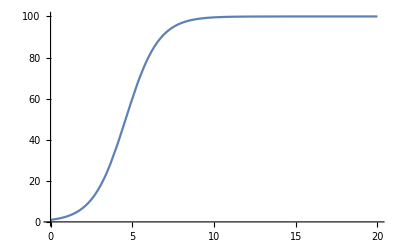

```mathematica
Plot[logistic[t,1, 100, 1],{t,0,20}]
```

```mathematica
D[logistic[t,α,κ,y0],α]
```

```mathematica
(ⅇ^(-t α) t κ (-y0+κ))/(y0 (1+(ⅇ^(-t α) (-y0+κ))/y0)^2)//FullSimplify
```

```mathematica
(ⅇ^(-t α) t κ (-y0+κ))/(y0 (1+(ⅇ^(-t α) (-y0+κ))/y0)^2)//TeXForm
```

\frac{\kappa  t e^{\alpha  (-t)} (\kappa -\text{y0})}{\text{y0} \left(\frac{e^{\alpha 
   (-t)} (\kappa -\text{y0})}{\text{y0}}+1\right)^2}

```mathematica
D[logistic[t,α,κ,y0],κ]//FullSimplify
```

```mathematica
(ⅇ^(t α) (-1+ⅇ^(t α)) y0^2)/(((-1+ⅇ^(t α)) y0+κ)^2)//TeXForm
```

\frac{\text{y0}^2 e^{\alpha  t} \left(e^{\alpha  t}-1\right)}{\left(\kappa +\text{y0}
   \left(e^{\alpha  t}-1\right)\right)^2}

```mathematica
D[(ⅇ^(-t α) t κ (-y0+κ))/(y0 (1+(ⅇ^(-t α) (-y0+κ))/y0)^2),α]
```

(2 ⅇ^(-2 t α) t^2 κ (-y0+κ)^2)/(y0^2 (1+(ⅇ^(-t α) (-y0+κ))/y0)^3)-(ⅇ^(-t α) t^2 κ (-y0+κ))/(y0 (1+(ⅇ^(-t α) (-y0+κ))/y0)^2)